```mathematica
(*This system will be a plate with a rod in the middle. 
This example will use Lie-Trotter Splitting
So the equation is F = R + V
R is the 2D plate without the rod
V is the 2D plate with the rod

Here is the pseudo-code:
Let F(0) = initV below
For t = 0,tau, 2tau,...,T
	 Let R(t) = F(t)
	Integrate R'(t) to obtain R(t+tau)
	Let V(t)=R(t+tau)
   Integrate V'(t) to obtain V(t+tau)
   Let F(t+tau)=V(t+tau) 	*)
```

```mathematica
initV[x_,y_]:=20*x(x-2)y(y-1)
```

```mathematica
Plot3D[initV[x,y],{x,0,2},{y,0,1}]
```

-Graphics3D-

```mathematica
alphaPlate = 0.05; alphaRod = 0.2;
```

```mathematica
maxT = 15; NN = 100; tau=maxT/NN; (*max time and num time steps respectively*)
```

```mathematica
u1vals = NDSolveValue[{{D[u[y,t],t]==alphaRod*D[u[y,t],{y,2}]},{u[y,0]==initV[1,y]},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,0,tau}]
```

InterpolatingFunction[{{0., 1.}, {0., 0.15}}, <>]

```mathematica
v1vals = NDSolveValue[{{D[v[x,y,t],t]==alphaPlate*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==-u1vals[y,tau]*x*(x-2)},{v[x,0,t]==0},{v[x,1,t]==0},{v[0,y,t]==0},{v[2,y,t]==0}},v,{x,0,2},{y,0,1},{t,0,tau}]
```

InterpolatingFunction[{{0., 2.}, {0., 1.}, {0., 0.15}}, <>]

```mathematica
u2vals =NDSolveValue[{{D[u[y,t],t]==alphaRod*D[u[y,t],{y,2}]},{u[y,tau]==v1vals[1,y,tau]},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,tau,2*tau}]
```

InterpolatingFunction[{{0., 1.}, {0.15, 0.3}}, <>]

```mathematica
v2vals = NDSolveValue[{{D[v[x,y,t],t]==alphaPlate*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,tau]==-u2vals[y,2*tau]*x*(x-2)},{v[x,0,t]==0},{v[x,1,t]==0},{v[0,y,t]==0},{v[2,y,t]==0}},v,{x,0,2},{y,0,1},{t,tau,2*tau}]
```

InterpolatingFunction[{{0., 2.}, {0., 1.}, {0.15, 0.3}}, <>]

```mathematica
list1 = Range[5]
```

{1,2,3,4,5}

```mathematica
AppendTo[list1,9]
```

{1,2,3,4,5,9}

```mathematica
Part[list1,5]
```

5

```mathematica
list1[[5]]
```

5

```mathematica
listR = Range[15]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
listV = Range[16,30]
```

{16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
listF={0}
```

{0}

```mathematica
Do[(rr = listF[[i]]; rr = rr + listR[[i]]; vv = listV[[i]]+rr; AppendTo[listF,vv]),{i,1,15}]
```

```mathematica
listF
```

{0,17,36,57,80,105,132,161,192,225,260,297,336,377,420,465}

```mathematica
initVals = NDSolveValue[{{y''[t]==-9.8},{y'[0]==0},{y[0]==0}},y,{t,0,10}]
```

InterpolatingFunction[{{0., 10.}}, <>]

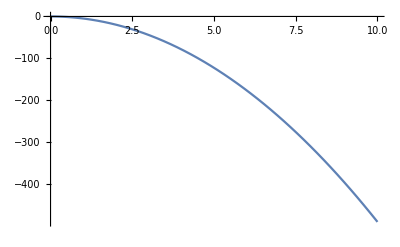

```mathematica
Plot[initVals[t],{t,0,10}]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
listVV = {0}
```

{0}

```mathematica
listVeloc = {0}
```

{0}

```mathematica
Do[(curY = listVV[[i]]; 
curVeloc = listVeloc[[i]];
vals = NDSolveValue[{{y''[t]==-9.8},{y'[0]==curVeloc},{y[0]==curY}},y,{t,0,1}];
vals2 = NDSolveValue[{{vel'[t]==-9.8},{vel[0]==curVeloc}},vel,{t,0,1}];
AppendTo[listVeloc,vals2[1]];
AppendTo[listVV,vals[1]]),{i,1,10}]
```

```mathematica
listVV
```

{0,-4.9,-19.6,-44.1,-78.4,-122.5,-176.4,-240.1,-313.6,-396.9,-490.}

```mathematica
(*The above example shows how to combine lists, for loops, and PDE solving*)
(*In the below I will try to use the heat equation on a simple 1D rod*)
```

```mathematica
curT[y_]:=-20*y*(y-1)
```

```mathematica
Do[(tvals = NDSolveValue[{{D[u[y,t],t]==alphaRod*D[u[y,t],{y,2}]},{u[y,0]==curT[y]},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,0,1}];curT[y_] := tvals[y,1]
),{i,1,10}]
```

```mathematica
(*Here I need to take the above and see if I can make a list of tables*)
```

```mathematica
initTvals = Table[curT[i/100],{i,0,100}]
```

{0,99/500,49/125,291/500,96/125,19/20,141/125,651/500,184/125,819/500,9/5,979/500,264/125,1131/500,301/125,51/20,336/125,1411/500,369/125,1539/500,16/5,1659/500,429/125,1771/500,456/125,15/4,481/125,1971/500,504/125,2059/500,21/5,2139/500,544/125,2211/500,561/125,91/20,576/125,2331/500,589/125,2379/500,24/5,2419/500,609/125,2451/500,616/125,99/20,621/125,2491/500,624/125,2499/500,5,2499/500,624/125,2491/500,621/125,99/20,616/125,2451/500,609/125,2419/500,24/5,2379/500,589/125,2331/500,576/125,91/20,561/125,2211/500,544/125,2139/500,21/5,2059/500,504/125,1971/500,481/125,15/4,456/125,1771/500,429/125,1659/500,16/5,1539/500,369/125,1411/500,336/125,51/20,301/125,1131/500,264/125,979/500,9/5,819/500,184/125,651/500,141/125,19/20,96/125,291/500,49/125,99/500,0}

```mathematica
listOfVals = {initTvals}
```

{{0,99/500,49/125,291/500,96/125,19/20,141/125,651/500,184/125,819/500,9/5,979/500,264/125,1131/500,301/125,51/20,336/125,1411/500,369/125,1539/500,16/5,1659/500,429/125,1771/500,456/125,15/4,481/125,1971/500,504/125,2059/500,21/5,2139/500,544/125,2211/500,561/125,91/20,576/125,2331/500,589/125,2379/500,24/5,2419/500,609/125,2451/500,616/125,99/20,621/125,2491/500,624/125,2499/500,5,2499/500,624/125,2491/500,621/125,99/20,616/125,2451/500,609/125,2419/500,24/5,2379/500,589/125,2331/500,576/125,91/20,561/125,2211/500,544/125,2139/500,21/5,2059/500,504/125,1971/500,481/125,15/4,456/125,1771/500,429/125,1659/500,16/5,1539/500,369/125,1411/500,336/125,51/20,301/125,1131/500,264/125,979/500,9/5,819/500,184/125,651/500,141/125,19/20,96/125,291/500,49/125,99/500,0}}

```mathematica
Do[(tvals = NDSolveValue[{{D[u[y,t],t]==alphaRod*D[u[y,t],{y,2}]},{u[y,0]==curT[y]},{u[0,t]==0},{u[1,t]==0}},u,{y,0,1},{t,0,1}];curT[y_] := tvals[y,1];
curTvals = Table[curT[jj/100],{jj,1,100}];
AppendTo[listOfVals,curTvals]
),{ii,1,10}]
```

```mathematica
listOfVals
```

{{0,99/500,49/125,291/500,96/125,19/20,141/125,651/500,184/125,819/500,9/5,979/500,264/125,1131/500,301/125,51/20,336/125,1411/500,369/125,1539/500,16/5,1659/500,429/125,1771/500,456/125,15/4,481/125,1971/500,504/125,2059/500,21/5,2139/500,544/125,2211/500,561/125,91/20,576/125,2331/500,589/125,2379/500,24/5,2419/500,609/125,2451/500,616/125,99/20,621/125,2491/500,624/125,2499/500,5,2499/500,624/125,2491/500,621/125,99/20,616/125,2451/500,609/125,2419/500,24/5,2379/500,589/125,2331/500,576/125,91/20,561/125,2211/500,544/125,2139/500,21/5,2059/500,504/125,1971/500,481/125,15/4,456/125,1771/500,429/125,1659/500,16/5,1539/500,369/125,1411/500,336/125,51/20,301/125,1131/500,264/125,979/500,9/5,819/500,184/125,651/500,141/125,19/20,96/125,291/500,49/125,99/500,0},{0.0225226,0.0450231,0.0674791,0.0898686,0.112169,0.134359,0.156417,0.17832,0.200047,0.221577,0.242888,0.263959,0.28477,0.3053,0.325528,0.345436,0.365002,0.384208,0.403035,0.421465,0.439478,0.457058,0.474186,0.490847,0.507023,0.522699,0.537859,0.552488,0.566572,0.580097,0.593049,0.605416,0.617186,0.628346,0.638887,0.648797,0.658066,0.666687,0.674649,0.681945,0.688569,0.694513,0.699771,0.704339,0.708212,0.711386,0.713858,0.715625,0.716686,0.71704,0.716686,0.715625,0.713858,0.711386,0.708212,0.704339,0.699771,0.694513,0.688569,0.681945,0.674649,0.666687,0.658066,0.648797,0.638887,0.628346,0.617186,0.605416,0.593049,0.580097,0.566572,0.552488,0.537859,0.522699,0.507023,0.490847,0.474186,0.457058,0.439478,0.421465,0.403035,0.384208,0.365002,0.345436,0.325528,0.3053,0.28477,0.263959,0.242888,0.221577,0.200047,0.17832,0.156417,0.134359,0.112169,0.0898686,0.0674791,0.0450231,0.0225226,0.},{0.00313182,0.00626056,0.00938312,0.0124964,0.0155974,0.018683,0.0217501,0.0247958,0.027817,0.0308107,0.0337741,0.0367041,0.0395979,0.0424526,0.0452654,0.0480336,0.0507543,0.053425,0.0560429,0.0586055,0.0611103,0.0635548,0.0659366,0.0682532,0.0705026,0.0726823,0.0747903,0.0768246,0.078783,0.0806636,0.0824646,0.0841843,0.0858209,0.0873728,0.0888384,0.0902164,0.0915054,0.092704,0.0938112,0.0948258,0.0957468,0.0965733,0.0973045,0.0979396,0.0984782,0.0989195,0.0992632,0.099509,0.0996565,0.0997057,0.0996565,0.099509,0.0992632,0.0989195,0.0984782,0.0979396,0.0973045,0.0965733,0.0957468,0.0948258,0.0938112,0.092704,0.0915054,0.0902164,0.0888384,0.0873728,0.0858209,0.0841843,0.0824646,0.0806636,0.078783,0.0768246,0.0747903,0.0726823,0.0705026,0.0682532,0.0659366,0.0635548,0.0611103,0.0586055,0.0560429,0.053425,0.0507543,0.0480336,0.0452654,0.0424526,0.0395979,0.0367041,0.0337741,0.0308107,0.027817,0.0247958,0.0217501,0.018683,0.0155974,0.0124964,0.00938312,0.00626056,0.00313182,0.},{0.000435603,0.000870777,0.00130509,0.00173812,0.00216943,0.0025986,0.00302521,0.00344883,0.00386904,0.00428544,0.00469761,0.00510515,0.00550764,0.0059047,0.00629593,0.00668095,0.00705938,0.00743084,0.00779497,0.0081514,0.00849979,0.00883979,0.00917107,0.00949329,0.00980615,0.0101093,0.0104025,0.0106855,0.0109579,0.0112194,0.0114699,0.0117091,0.0119368,0.0121526,0.0123565,0.0125481,0.0127274,0.0128941,0.0130481,0.0131892,0.0133173,0.0134323,0.013534,0.0136223,0.0136973,0.0137586,0.0138064,0.0138406,0.0138611,0.013868,0.0138611,0.0138406,0.0138064,0.0137586,0.0136973,0.0136223,0.013534,0.0134323,0.0133173,0.0131892,0.0130481,0.0128941,0.0127274,0.0125481,0.0123565,0.0121526,0.0119368,0.0117091,0.0114699,0.0112194,0.0109579,0.0106855,0.0104025,0.0101093,0.00980615,0.00949329,0.00917107,0.00883979,0.00849979,0.0081514,0.00779497,0.00743084,0.00705938,0.00668095,0.00629593,0.0059047,0.00550764,0.00510515,0.00469761,0.00428544,0.00386904,0.00344883,0.00302521,0.0025986,0.00216943,0.00173812,0.00130509,0.000870777,0.000435603,0.},{0.000060388,0.000120717,0.000180926,0.000240957,0.00030075,0.000360246,0.000419387,0.000478114,0.000536369,0.000594095,0.000651234,0.000707731,0.000763529,0.000818574,0.000872811,0.000926186,0.000978648,0.00103014,0.00108062,0.00113004,0.00117833,0.00122547,0.00127139,0.00131606,0.00135943,0.00140146,0.00144211,0.00148134,0.0015191,0.00155536,0.00159009,0.00162325,0.0016548,0.00168473,0.00171299,0.00173956,0.00176441,0.00178752,0.00180887,0.00182844,0.00184619,0.00186213,0.00187623,0.00188848,0.00189886,0.00190737,0.001914,0.00191874,0.00192158,0.00192253,0.00192158,0.00191874,0.001914,0.00190737,0.00189886,0.00188848,0.00187623,0.00186213,0.00184619,0.00182844,0.00180887,0.00178752,0.00176441,0.00173956,0.00171299,0.00168473,0.0016548,0.00162325,0.00159009,0.00155536,0.0015191,0.00148134,0.00144211,0.00140146,0.00135943,0.00131606,0.00127139,0.00122547,0.00117833,0.00113004,0.00108062,0.00103014,0.000978648,0.000926186,0.000872811,0.000818574,0.000763529,0.000707731,0.000651234,0.000594095,0.000536369,0.000478114,0.000419387,0.000360246,0.00030075,0.000240957,0.000180926,0.000120717,0.000060388,0.},{8.35114×10^-6,0.0000166941,0.0000250205,0.0000333223,0.0000415911,0.0000498189,0.0000579976,0.000066119,0.0000741752,0.0000821582,0.0000900601,0.0000978731,0.000105589,0.000113202,0.000120702,0.000128084,0.000135339,0.00014246,0.000149441,0.000156274,0.000162953,0.000169472,0.000175823,0.000182,0.000187998,0.000193811,0.000199432,0.000204856,0.000210078,0.000215093,0.000219896,0.000224481,0.000228845,0.000232983,0.000236891,0.000240566,0.000244003,0.000247199,0.000250152,0.000252857,0.000255313,0.000257517,0.000259467,0.00026116,0.000262596,0.000263773,0.00026469,0.000265345,0.000265738,0.00026587,0.000265738,0.000265345,0.00026469,0.000263773,0.000262596,0.00026116,0.000259467,0.000257517,0.000255313,0.000252857,0.000250152,0.000247199,0.000244003,0.000240566,0.000236891,0.000232983,0.000228845,0.000224481,0.000219896,0.000215093,0.000210078,0.000204856,0.000199432,0.000193811,0.000187998,0.000182,0.000175823,0.000169472,0.000162953,0.000156274,0.000149441,0.00014246,0.000135339,0.000128084,0.000120702,0.000113202,0.000105589,0.0000978731,0.0000900601,0.0000821582,0.0000741752,0.000066119,0.0000579976,0.0000498189,0.0000415911,0.0000333223,0.0000250205,0.0000166941,8.35114×10^-6,0.},{1.32651×10^-6,2.65171×10^-6,3.97429×10^-6,5.29296×10^-6,6.6064×10^-6,7.91332×10^-6,9.21243×10^-6,0.0000105024,0.0000117821,0.0000130501,0.0000143053,0.0000155463,0.000016772,0.0000179811,0.0000191725,0.000020345,0.0000214974,0.0000226286,0.0000237374,0.0000248228,0.0000258837,0.0000269191,0.0000279279,0.0000289092,0.0000298619,0.0000307851,0.000031678,0.0000325396,0.0000333691,0.0000341657,0.0000349285,0.0000356569,0.0000363501,0.0000370074,0.0000376282,0.0000382118,0.0000387578,0.0000392655,0.0000397344,0.0000401642,0.0000405543,0.0000409043,0.000041214,0.0000414831,0.0000417112,0.0000418981,0.0000420437,0.0000421478,0.0000422103,0.0000422311,0.0000422103,0.0000421478,0.0000420437,0.0000418981,0.0000417112,0.0000414831,0.000041214,0.0000409043,0.0000405543,0.0000401642,0.0000397344,0.0000392655,0.0000387578,0.0000382118,0.0000376282,0.0000370074,0.0000363501,0.0000356569,0.0000349285,0.0000341657,0.0000333691,0.0000325396,0.000031678,0.0000307851,0.0000298619,0.0000289092,0.0000279279,0.0000269191,0.0000258837,0.0000248228,0.0000237374,0.0000226286,0.0000214974,0.000020345,0.0000191725,0.0000179811,0.000016772,0.0000155463,0.0000143053,0.0000130501,0.0000117821,0.0000105024,9.21243×10^-6,7.91332×10^-6,6.6064×10^-6,5.29296×10^-6,3.97429×10^-6,2.65171×10^-6,1.32651×10^-6,0.},{2.10722×10^-7,4.21237×10^-7,6.31336×10^-7,8.40812×10^-7,1.04946×10^-6,1.25707×10^-6,1.46344×10^-6,1.66837×10^-6,1.87164×10^-6,2.07308×10^-6,2.27246×10^-6,2.46961×10^-6,2.66431×10^-6,2.85639×10^-6,3.04565×10^-6,3.2319×10^-6,3.41497×10^-6,3.59466×10^-6,3.7708×10^-6,3.94323×10^-6,4.11176×10^-6,4.27624×10^-6,4.43649×10^-6,4.59237×10^-6,4.74371×10^-6,4.89037×10^-6,5.03221×10^-6,5.16908×10^-6,5.30085×10^-6,5.42739×10^-6,5.54857×10^-6,5.66428×10^-6,5.77439×10^-6,5.87881×10^-6,5.97742×10^-6,6.07014×10^-6,6.15687×10^-6,6.23752×10^-6,6.31201×10^-6,6.38028×10^-6,6.44225×10^-6,6.49786×10^-6,6.54705×10^-6,6.58979×10^-6,6.62603×10^-6,6.65572×10^-6,6.67885×10^-6,6.69538×10^-6,6.70531×10^-6,6.70862×10^-6,6.70531×10^-6,6.69538×10^-6,6.67885×10^-6,6.65572×10^-6,6.62603×10^-6,6.58979×10^-6,6.54705×10^-6,6.49786×10^-6,6.44225×10^-6,6.38028×10^-6,6.31201×10^-6,6.23752×10^-6,6.15687×10^-6,6.07014×10^-6,5.97742×10^-6,5.87881×10^-6,5.77439×10^-6,5.66428×10^-6,5.54857×10^-6,5.42739×10^-6,5.30085×10^-6,5.16908×10^-6,5.03221×10^-6,4.89037×10^-6,4.74371×10^-6,4.59237×10^-6,4.43649×10^-6,4.27624×10^-6,4.11176×10^-6,3.94323×10^-6,3.7708×10^-6,3.59466×10^-6,3.41497×10^-6,3.2319×10^-6,3.04565×10^-6,2.85639×10^-6,2.66431×10^-6,2.46961×10^-6,2.27246×10^-6,2.07308×10^-6,1.87164×10^-6,1.66837×10^-6,1.46344×10^-6,1.25707×10^-6,1.04946×10^-6,8.40812×10^-7,6.31336×10^-7,4.21237×10^-7,2.10722×10^-7,0.},{3.35245×10^-8,6.70159×10^-8,1.00441×10^-7,1.33767×10^-7,1.66962×10^-7,1.99991×10^-7,2.32823×10^-7,2.65425×10^-7,2.97766×10^-7,3.29812×10^-7,3.61533×10^-7,3.92897×10^-7,4.23874×10^-7,4.54432×10^-7,4.84542×10^-7,5.14173×10^-7,5.43297×10^-7,5.71885×10^-7,5.99909×10^-7,6.2734×10^-7,6.54153×10^-7,6.80319×10^-7,7.05815×10^-7,7.30614×10^-7,7.54692×10^-7,7.78025×10^-7,8.0059×10^-7,8.22365×10^-7,8.43329×10^-7,8.6346×10^-7,8.82739×10^-7,9.01147×10^-7,9.18666×10^-7,9.35278×10^-7,9.50967×10^-7,9.65717×10^-7,9.79515×10^-7,9.92346×10^-7,1.0042×10^-6,1.01506×10^-6,1.02492×10^-6,1.03376×10^-6,1.04159×10^-6,1.04839×10^-6,1.05415×10^-6,1.05888×10^-6,1.06256×10^-6,1.06519×10^-6,1.06677×10^-6,1.0673×10^-6,1.06677×10^-6,1.06519×10^-6,1.06256×10^-6,1.05888×10^-6,1.05415×10^-6,1.04839×10^-6,1.04159×10^-6,1.03376×10^-6,1.02492×10^-6,1.01506×10^-6,1.0042×10^-6,9.92346×10^-7,9.79515×10^-7,9.65717×10^-7,9.50967×10^-7,9.35278×10^-7,9.18666×10^-7,9.01147×10^-7,8.82739×10^-7,8.6346×10^-7,8.43329×10^-7,8.22365×10^-7,8.0059×10^-7,7.78025×10^-7,7.54692×10^-7,7.30614×10^-7,7.05815×10^-7,6.80319×10^-7,6.54153×10^-7,6.2734×10^-7,5.99909×10^-7,5.71885×10^-7,5.43297×10^-7,5.14173×10^-7,4.84542×10^-7,4.54432×10^-7,4.23874×10^-7,3.92897×10^-7,3.61533×10^-7,3.29812×10^-7,2.97766×10^-7,2.65425×10^-7,2.32823×10^-7,1.99991×10^-7,1.66962×10^-7,1.33767×10^-7,1.00441×10^-7,6.70159×10^-8,3.35245×10^-8,0.},{5.33007×10^-9,1.06549×10^-8,1.59692×10^-8,2.12678×10^-8,2.65453×10^-8,3.17967×10^-8,3.70167×10^-8,4.22001×10^-8,4.73419×10^-8,5.2437×10^-8,5.74804×10^-8,6.2467×10^-8,6.73919×10^-8,7.22504×10^-8,7.70376×10^-8,8.17487×10^-8,8.63791×10^-8,9.09243×10^-8,9.53798×10^-8,9.97412×10^-8,1.04004×10^-7,1.08164×10^-7,1.12218×10^-7,1.16161×10^-7,1.19989×10^-7,1.23699×10^-7,1.27286×10^-7,1.30748×10^-7,1.34081×10^-7,1.37282×10^-7,1.40347×10^-7,1.43274×10^-7,1.46059×10^-7,1.487×10^-7,1.51195×10^-7,1.5354×10^-7,1.55734×10^-7,1.57774×10^-7,1.59658×10^-7,1.61385×10^-7,1.62952×10^-7,1.64359×10^-7,1.65603×10^-7,1.66684×10^-7,1.67601×10^-7,1.68352×10^-7,1.68937×10^-7,1.69355×10^-7,1.69606×10^-7,1.6969×10^-7,1.69606×10^-7,1.69355×10^-7,1.68937×10^-7,1.68352×10^-7,1.67601×10^-7,1.66684×10^-7,1.65603×10^-7,1.64359×10^-7,1.62952×10^-7,1.61385×10^-7,1.59658×10^-7,1.57774×10^-7,1.55734×10^-7,1.5354×10^-7,1.51195×10^-7,1.487×10^-7,1.46059×10^-7,1.43274×10^-7,1.40347×10^-7,1.37282×10^-7,1.34081×10^-7,1.30748×10^-7,1.27286×10^-7,1.23699×10^-7,1.19989×10^-7,1.16161×10^-7,1.12218×10^-7,1.08164×10^-7,1.04004×10^-7,9.97412×10^-8,9.53798×10^-8,9.09243×10^-8,8.63791×10^-8,8.17487×10^-8,7.70376×10^-8,7.22504×10^-8,6.73919×10^-8,6.2467×10^-8,5.74804×10^-8,5.2437×10^-8,4.73419×10^-8,4.22001×10^-8,3.70167×10^-8,3.17967×10^-8,2.65453×10^-8,2.12678×10^-8,1.59692×10^-8,1.06549×10^-8,5.33007×10^-9,0.},{8.32351×10^-10,1.66388×10^-9,2.49377×10^-9,3.3212×10^-9,4.14535×10^-9,4.96541×10^-9,5.78057×10^-9,6.59003×10^-9,7.39298×10^-9,8.18864×10^-9,8.97621×10^-9,9.75493×10^-9,1.0524×10^-8,1.12827×10^-8,1.20303×10^-8,1.2766×10^-8,1.34891×10^-8,1.41989×10^-8,1.48946×10^-8,1.55757×10^-8,1.62414×10^-8,1.68911×10^-8,1.75241×10^-8,1.81398×10^-8,1.87376×10^-8,1.93169×10^-8,1.98772×10^-8,2.04178×10^-8,2.09383×10^-8,2.14381×10^-8,2.19168×10^-8,2.23738×10^-8,2.28088×10^-8,2.32212×10^-8,2.36108×10^-8,2.3977×10^-8,2.43196×10^-8,2.46381×10^-8,2.49324×10^-8,2.5202×10^-8,2.54468×10^-8,2.56665×10^-8,2.58608×10^-8,2.60296×10^-8,2.61728×10^-8,2.629×10^-8,2.63814×10^-8,2.64467×10^-8,2.64859×10^-8,2.6499×10^-8,2.64859×10^-8,2.64467×10^-8,2.63814×10^-8,2.629×10^-8,2.61728×10^-8,2.60296×10^-8,2.58608×10^-8,2.56665×10^-8,2.54468×10^-8,2.5202×10^-8,2.49324×10^-8,2.46381×10^-8,2.43196×10^-8,2.3977×10^-8,2.36108×10^-8,2.32212×10^-8,2.28088×10^-8,2.23738×10^-8,2.19168×10^-8,2.14381×10^-8,2.09383×10^-8,2.04178×10^-8,1.98772×10^-8,1.93169×10^-8,1.87376×10^-8,1.81398×10^-8,1.75241×10^-8,1.68911×10^-8,1.62414×10^-8,1.55757×10^-8,1.48946×10^-8,1.41989×10^-8,1.34891×10^-8,1.2766×10^-8,1.20303×10^-8,1.12827×10^-8,1.0524×10^-8,9.75493×10^-9,8.97621×10^-9,8.18864×10^-9,7.39298×10^-9,6.59003×10^-9,5.78057×10^-9,4.96541×10^-9,4.14535×10^-9,3.3212×10^-9,2.49377×10^-9,1.66388×10^-9,8.32351×10^-10,0.}}

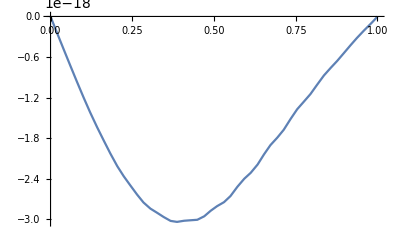

```mathematica
Plot[{curT[y]},{y,0,1}]
```

```mathematica
ff[x_]:=-10*x*(x-1)
```

```mathematica
listInit = {ff}
```

{ff}

```mathematica
gg[x_]:=-20*x*(x-1)
```

```mathematica
AppendTo[listInit,gg]
```

{ff,gg}

```mathematica
(f1 = listInit[[1]]; f1[2])
```

-20

```mathematica
aa = Evaluate[-10*x*(x-1),{x,0,1}]
```

Sequence[-10 (-1+x) x,{x,0,1}]

```mathematica
Table[i^2,{i,1,5}]
```

{1,4,9,16,25}